```mathematica
AudicClaverie[x_,y_,N1_,N2_]:=((N2/N1)^y)(Gamma[x+y+1]/(Gamma[x+1]Gamma[y+1](1+N2/N1)^(x+y+1)))
```

```mathematica
Manipulate[Plot[AudicClaverie[x,y,100,100],{y,0,20},Filling->Bottom],{x,0,10}]
```

```mathematica
LogAudicClaverie[x_,y_,N1_,N2_]:=y Log[N2/N1]+LogGamma[x+y+1]-LogGamma[x+1]-LogGamma[y+1]-(x+y+1)Log[1+N2/N1]
```

```mathematica
Manipulate[Plot[LogAudicClaverie[x,y,100,100],{y,0,20},Filling->Bottom],{x,0,10}]
```

```mathematica
Integrate[(B^-A ⅇ^(-L1/B) L1^(-1+A))/Gamma[A](ⅇ^-L1 L1^x)/(x!),{L1,0,Infinity},Assumptions->{A>0,B>0,x≥0}]
```

(B^x (1+B)^(-A-x) Gamma[A+x])/(x! Gamma[A])

```mathematica
Integrate[(B^-A ⅇ^(-L1/B) L1^(-1+A))/Gamma[A](B^-A ⅇ^(-L2/B) L2^(-1+A))/Gamma[A](ⅇ^-L1 L1^x)/(x!)(ⅇ^-L2 L2^y)/(y!),{L1,0,Infinity},{L2,0,Infinity},Assumptions->{A>0,B>0,x≥0,y≥0}]
```

((B/(1+B))^(x+y) (1+B)^(-2 A) Gamma[A+x] Gamma[A+y])/(x! y! Gamma[A]^2)

```mathematica
Integrate[(B^-A ⅇ^(-L1/B) L1^(-1+A))/Gamma[A](ⅇ^-L1 L1^x)/(x!)(ⅇ^-L1 L1^y)/(y!),{L1,0,Infinity},Assumptions->{A>0,B>0,x≥0,y≥0}]
```

(B^-A (B/(1+2 B))^(A+x+y) Gamma[A+x+y])/(x! y! Gamma[A])

```mathematica
BF[A_,B_,x_,y_]:=(B^-A (B/(1+2 B))^(A+x+y) Gamma[A+x+y])/(x! y! Gamma[A])/(((B/(1+B))^(x+y) (1+B)^(-2 A) Gamma[A+x] Gamma[A+y])/(x! y! Gamma[A]^2))
```

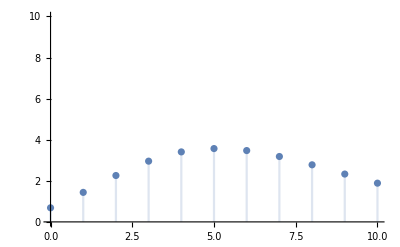

```mathematica
DiscretePlot[BF[2,10,6,n],{n,0,10},PlotRange->{All,{0,10}}]
```

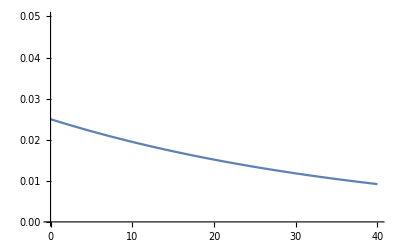

```mathematica
Plot[PDF[GammaDistribution[1,40],x],{x,0,40},PlotRange->{All,{0,0.05}}]
```

```mathematica
Integrate[(B^-A ⅇ^(-L1/B) L1^(-1+A))/Gamma[A](B^-A ⅇ^(-L2/B) L2^(-1+A))/Gamma[A](ⅇ^-L1 L1^x)/(x!)(ⅇ^-L2 L2^y)/(y!)(ⅇ^-L1 L1^z)/(z!)(ⅇ^-L2 L2^w)/(w!),{L1,0,Infinity},{L2,0,Infinity},Assumptions->{A>0,B>0,x≥0,y≥0,z≥0,w≥0}]
```

(B^(-2 A) (B/(1+2 B))^(2 A+w+x+y+z) Gamma[A+w+y] Gamma[A+x+z])/(w! x! y! z! Gamma[A]^2)

```mathematica
Integrate[(B^-A ⅇ^(-L1/B) L1^(-1+A))/Gamma[A](B^-A ⅇ^(-L2/B) L2^(-1+A))/Gamma[A](B^-A ⅇ^(-L3/B) L3^(-1+A))/Gamma[A](B^-A ⅇ^(-L4/B) L4^(-1+A))/Gamma[A](ⅇ^-L1 L1^x)/(x!)(ⅇ^-L2 L2^y)/(y!)(ⅇ^-L3 L3^z)/(z!)(ⅇ^-L4 L4^w)/(w!),{L1,0,Infinity},{L2,0,Infinity},{L3,0,Infinity},{L4,0,Infinity},Assumptions->{A>0,B>0,x≥0,y≥0,z≥0,w≥0}]
```

((B/(1+B))^(w+x+y+z) (1+B)^(-4 A) Gamma[A+w] Gamma[A+x] Gamma[A+y] Gamma[A+z])/(w! x! y! z! Gamma[A]^4)

```mathematica
BF[A_,B_,{x_,y_},{z_,w_}]:=(B^(-2 A) (B/(1+2 B))^(2 A+w+x+y+z) Gamma[A+w+y] Gamma[A+x+z])/(w! x! y! z! Gamma[A]^2)/(((B/(1+B))^(w+x+y+z) (1+B)^(-4 A) Gamma[A+w] Gamma[A+x] Gamma[A+y] Gamma[A+z])/(w! x! y! z! Gamma[A]^4))
```

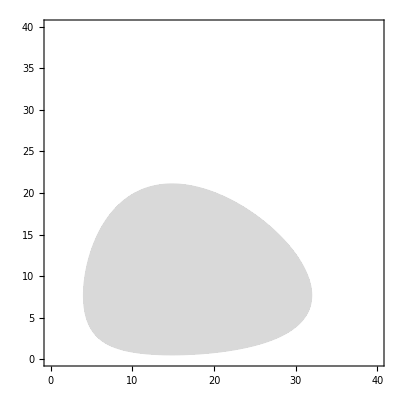

```mathematica
With[{x=15,y=8},DensityPlot[BF[1,40,{x,y},{z,w}],{z,0,40},{w,0,40},ColorFunction->(LightGray&),RegionFunction->Function[{z,w,p},BF[1,40,{x,y},{z,w}]>1],BoundaryStyle->Red]]
```

```mathematica
Exp[Log[B^(-2 A) (B/(1+2 B))^(2 A+w+x+y+z)]+LogGamma[A+w+y]+LogGamma[A+x+z]-LogGamma[w+1]-LogGamma[x+1]-LogGamma[y+1]-LogGamma[z+1]-2LogGamma[A]]
```

```mathematica
BF[A_,B_,{x_,y_},{z_,w_}]:=Exp[-2A Log[B]+(2 A+w+x+y+z)Log[ B/(1+2 B)]+LogGamma[A+w+y]+LogGamma[A+x+z]-LogGamma[w+1]-LogGamma[x+1]-LogGamma[y+1]-LogGamma[z+1]-2LogGamma[A]]/(((B/(1+B))^(w+x+y+z) (1+B)^(-4 A) Gamma[A+w] Gamma[A+x] Gamma[A+y] Gamma[A+z])/(w! x! y! z! Gamma[A]^4))
```

```mathematica
-2A Log[B]+(2 A+w+x+y+z)Log[ B/(1+2 B)]
```

Log[B^(-2 A) (B/(1+2 B))^(2 A+w+x+y+z)]

```mathematica
BF[A_,B_,x_,y_]:=(B^-A (B/(1+2 B))^(A+x+y) Gamma[A+x+y])/(x! y! Gamma[A])/(((B/(1+B))^(x+y) (1+B)^(-2 A) Gamma[A+x] Gamma[A+y])/(x! y! Gamma[A]^2))
```

```mathematica
BF3[A_,B_,{x_,y_,j_},{z_,w_,v_}]:=(B^(-3 A) (B/(1+2 B))^(3 A+v.+w+x+y+z+j) Gamma[A+v+j] Gamma[A+w+y] Gamma[A+x+z])/(v!j!w! x! y! z! Gamma[A]^3)/(((B/(1+B))^(w+x+y+z+v+j) (1+B)^(-6 A) Gamma[A+v]Gamma[A+j]Gamma[A+w] Gamma[A+x] Gamma[A+y] Gamma[A+z])/(j!v!w! x! y! z! Gamma[A]^6))
```

```mathematica
With[{x=13,y=9,j=13},RegionPlot3D[BF3[1,40,{x,y,j},{z,w,v}]>1,{z,0,40},{w,0,40},{v,0,40}, PlotLegends->Automatic]]
```

-Graphics3D-

#### Single Poisson distribution, with size factor

In three dimensions

```mathematica
Integrate[(B^-A ⅇ^(-L1/B) L1^(-1+A))/Gamma[A](B^-A ⅇ^(-L2/B) L2^(-1+A))/Gamma[A](B^-A ⅇ^(-L3/B) L3^(-1+A))/Gamma[A](ⅇ^(-(C L1)) (C L1)^x)/(x!)(ⅇ^(-(C L2)) (C L2)^y)/(y!)(ⅇ^(-(C L3)) (C L3)^z)/(z!)(ⅇ^-L1 L1^u)/(u!)(ⅇ^-L2 L2^v)/(v!)(ⅇ^-L3 L3^w)/(w!),{L1,0,Infinity},{L2,0,Infinity},{L3,0,Infinity},Assumptions->{A>0,B>0,x≥0,y≥0,z≥0,u≥0,v≥0,w≥0,C≥0}]
```

(C^(x+y+z) (B/(1+B+B C))^(u+v+w+x+y+z) (1+B+B C)^(-3 A) Gamma[A+u+x] Gamma[A+v+y] Gamma[A+w+z])/(u! v! w! x! y! z! Gamma[A]^3)

In two dimensions

```mathematica
Integrate[(B^-A ⅇ^(-L1/B) L1^(-1+A))/Gamma[A](B^-A ⅇ^(-L2/B) L2^(-1+A))/Gamma[A](ⅇ^(-(C L1)) (C L1)^x)/(x!)(ⅇ^(-(C L2)) (C L2)^y)/(y!)(ⅇ^-L1 L1^u)/(u!)(ⅇ^-L2 L2^v)/(v!),{L1,0,Infinity},{L2,0,Infinity},Assumptions->{A>0,B>0,x≥0,y≥0,u≥0,v≥0,C≥0}]
```

(B^(u+v+x+y) C^(x+y) (1+B+B C)^(-2 A-u-v-x-y) Gamma[A+u+x] Gamma[A+v+y])/(u! v! x! y! Gamma[A]^2)

In one dimension

```mathematica
Integrate[(B^-A ⅇ^(-L1/B) L1^(-1+A))/Gamma[A](ⅇ^(-(C L1)) (C L1)^x)/(x!)(ⅇ^-L1 L1^u)/(u!),{L1,0,Infinity},Assumptions->{A>0,B>0,x≥0,u≥0,C≥0}]
```

(B^-A C^x (B/(1+B+B C))^(A+u+x) Gamma[A+u+x])/(u! x! Gamma[A])

#### Two independent Poisson distributions, with size factor

Three dimensions

```mathematica
Integrate[(B^-A ⅇ^(-L1/B) L1^(-1+A))/Gamma[A](B^-A ⅇ^(-L2/B) L2^(-1+A))/Gamma[A](B^-A ⅇ^(-L3/B) L3^(-1+A))/Gamma[A](B^-A ⅇ^(-L4/B) L4^(-1+A))/Gamma[A](B^-A ⅇ^(-L5/B) L5^(-1+A))/Gamma[A](B^-A ⅇ^(-L6/B) L6^(-1+A))/Gamma[A](ⅇ^(-(C L1)) (C L1)^x)/(x!)(ⅇ^(-(C L2))(C L2)^y)/(y!)(ⅇ^(-(C L3))(C L3)^z)/(z!)(ⅇ^-L4 L4^u)/(u!)(ⅇ^-L5 L5^v)/(v!)(ⅇ^-L6 L6^w)/(w!),{L1,0,Infinity},{L2,0,Infinity},{L3,0,Infinity},{L4,0,Infinity},{L5,0,Infinity},{L6,0,Infinity},Assumptions->{A>0,B>0,C>0,x≥0,y≥0,z≥0,u≥0,v≥0,w≥0}]
```

((B/(1+B))^(u+v+w) ((B C)/(1+B C))^(x+y+z) ((1+B) (1+B C))^(-3 A) Gamma[A+u] Gamma[A+v] Gamma[A+w] Gamma[A+x] Gamma[A+y] Gamma[A+z])/(u! v! w! x! y! z! Gamma[A]^6)

Two dimensions

```mathematica
Integrate[(B^-A ⅇ^(-L1/B) L1^(-1+A))/Gamma[A](B^-A ⅇ^(-L2/B) L2^(-1+A))/Gamma[A](B^-A ⅇ^(-L4/B) L4^(-1+A))/Gamma[A](B^-A ⅇ^(-L5/B) L5^(-1+A))/Gamma[A](ⅇ^(-(C L1)) (C L1)^x)/(x!)(ⅇ^(-(C L2))(C L2)^y)/(y!)(ⅇ^-L4 L4^u)/(u!)(ⅇ^-L5 L5^v)/(v!),{L1,0,Infinity},{L2,0,Infinity},{L4,0,Infinity},{L5,0,Infinity},Assumptions->{A>0,B>0,C>0,x≥0,y≥0,u≥0,v≥0}]
```

((B/(1+B))^(u+v) ((B C)/(1+B C))^(x+y) ((1+B) (1+B C))^(-2 A) Gamma[A+u] Gamma[A+v] Gamma[A+x] Gamma[A+y])/(u! v! x! y! Gamma[A]^4)

#### Bayes factor

```mathematica
(C^(x+y+z) (B/(1+B+B C))^(u+v+w+x+y+z) (1+B+B C)^(-3 A) Gamma[A+u+x] Gamma[A+v+y] Gamma[A+w+z])/(u! v! w! x! y! z! Gamma[A]^3)/(((B/(1+B))^(u+v+w) ((B C)/(1+B C))^(x+y+z) ((1+B) (1+B C))^(-3 A) Gamma[A+u] Gamma[A+v] Gamma[A+w] Gamma[A+x] Gamma[A+y] Gamma[A+z])/(u! v! w! x! y! z! Gamma[A]^6))
```

((B/(1+B))^(-u-v-w) C^(x+y+z) ((B C)/(1+B C))^(-x-y-z) ((1+B) (1+B C))^(3 A) (B/(1+B+B C))^(u+v+w+x+y+z) (1+B+B C)^(-3 A) Gamma[A]^3 Gamma[A+u+x] Gamma[A+v+y] Gamma[A+w+z])/(Gamma[A+u] Gamma[A+v] Gamma[A+w] Gamma[A+x] Gamma[A+y] Gamma[A+z])